```mathematica
SetDirectory[NotebookDirectory[]];
```

## Importing data

```mathematica
(*numerical solution, flag == 0, exact solution, flag == 1 and error flag == 2*)
importdata[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/solution/numerical_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 1,
filename=StringJoin["../",outputdir,"/solution/exact_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 2,
filename=StringJoin["..",outputdir,"/solution/error",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]]
];

result = Import[filename,"Table"][[2;;-1,All]]
]
```

## Solution

### G26 A

```mathematica
solution = importdata[4800,1,"_global_",0,"output_trial"];
ListPlot3D[solution⟦All,{1,2,3}⟧,PlotRange->All,ClippingStyle->True,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],Mesh->True,InterpolationOrder->3,ImageSize->400,PlotLabel->"deviation of temperature",PlotLegends->Automatic,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

### G26

#### exact solution

```mathematica
(*theta,delta,q,sigma,R,m*)
U26θW1[x_] :={-1.3193576588506577-0.548685702383432 x^2+0.13608276348795437 x^4+0.09005797246678635 Cosh[2.191140660407265 x]-6.938893903907228*^-18 Sinh[2.191140660407265 x],-0.21908902300206642 x^2,-1/3 √(2/5) x^3,-0.07331283107342124-0.1131370849898476 x^2+0.06499374330796374 Cosh[2.191140660407265 x],0.03918735656159667+0.21166010488516723 x^2-0.03474061710604745 Cosh[2.191140660407265 x],0.+0.14109060918431104 x-0.05708465895189606 Sinh[2.191140660407265 x]};

U26θW0[x_]:={-0.09461278745906829-0.548685702383432 x^2+0.13608276348795437 x^4+0.09005797246678635 Cosh[2.191140660407265 x],-0.21908902300206642 x^2,-1/3 √(2/5) x^3,-0.07331283107342124-0.1131370849898476 x^2+0.06499374330796374 Cosh[2.191140660407265 x],0.03918735656159667+0.21166010488516723 x^2-0.03474061710604745 Cosh[2.191140660407265 x],0.14109060918431104 x-0.05708465895189606 Sinh[2.191140660407265 x]};
```

#### Numerical solution

```mathematica
solution = importdata[61200,1,"_global_",0,"output_trial_G26"];
(*rho,vx,vy,θ,σxx,σxy,σyy,qx,qy,mxxx,mxxy,mxyy,myyy,Δ,Rxx,Rxy,Ryy*)

ListPlot3D[-√(2/3)solution⟦All,{1,2,6}⟧,PlotRange->{All,{-0.5,0.5}},ClippingStyle->True,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],Mesh->True,InterpolationOrder->3,ImageSize->400,PlotLabel->"deviation of temperature",PlotLegends->Automatic,AxesLabel->{"x","y","z"}]

ListPlot3D[solution⟦All,{1,2,11}⟧,PlotRange->All,ClippingStyle->True,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],Mesh->True,InterpolationOrder->3,ImageSize->400,PlotLabel->"heat flux",PlotLegends->Automatic,AxesLabel->{"x","y","z"}]


ListPlot3D[solution⟦All,{1,2,5}⟧,PlotRange->All,ClippingStyle->True,ColorFunction->Function[{x,y,z},ColorData["SouthwestColors"][z]],Mesh->True,InterpolationOrder->3,ImageSize->400,PlotLabel->"vy",PlotLegends->Automatic,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
N[Sqrt[2/3],15]
```

0.816496580927726

```mathematica
-2/1.3+3
```

1.46154

```mathematica
solution
```

{{-1.,-1.,-1.92612,0.,0.002518,0.222377,-0.743835,0.,1.48767,0.,0.206851,0.,-0.645376,0.,1.29075,-0.218214,0.322306,0.,-0.644611},{-0.333333,-1.,-1.92612,0.,0.002518,0.222377,-0.743835,0.,1.48767,0.,0.206851,0.,-0.645376,0.,1.29075,-0.218214,0.322306,0.,-0.644611},5996,{0.333333,1.,-1.92612,0.,-0.002518,0.222377,-0.743835,0.,1.48767,0.,-0.206851,0.,0.645376,0.,-1.29075,-0.218214,0.322306,0.,-0.644611},{1.,1.,-1.92612,0.,-0.002518,0.222377,-0.743835,0.,1.48767,0.,-0.206851,0.,0.645376,0.,-1.29075,-0.218214,0.322306,0.,-0.644611}}
 |  |  |  |

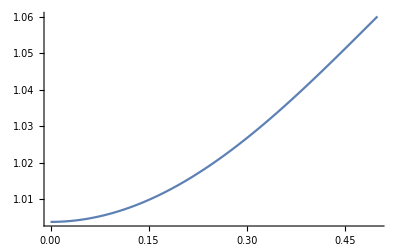

```mathematica
Plot[-√(2/3)U26θW1[x]⟦1⟧,{x,0,0.5}]
```